# Asymptotics and Steepest Descnet (chapter 12)

```mathematica
n=27560005;
(n!)/(√(2.0 π n) (n/ⅇ)^n)
```

1.00000000302371

### PreCalc

In you pre calculus class you learned about asymptotes etc.  You probably even used the tilde notation.  You were writing things like this
	f_1[x]=(3x+2 x^2)/(7 x^3+2x-1/x)~(0+2 x^2)/(7 x^3+0-0)=2/(7x) as |x|→∞
and 
	f2[x]=(3x+2 x^2+6 x^4)/(7 x^3+2x-1/x)~(6 x^4)/(7 x^3+0-0)=(6 x)/7 as |x|→∞
and you illustrated them as well.

Why did you want to do this?

```mathematica
f1[x_]:=(3x+2 x^2)/(7 x^3+2x-1/x)
g1[x_]:=2/(7 x)
f2[x_]:=(3x+2 x^2+6 x^4)/(7 x^3+2x-1/x) 
g2[x_]:=6 x/7
TabView[{
"f/g"->LogLogPlot[ {1,f1[x]/g1[x],f2[x]/g2[x]},{x,0,100},GridLines->Automatic,
PlotLegends->"Expressions"],
"|f/g-1|"->LogLogPlot[ {Abs[f1[x]/g1[x]-1],Abs[f2[x]/g2[x]-1]},{x,100,10^5},GridLines->Automatic,
PlotLegends->"Expressions"]}]
```

12

### Complex Analysis

Same thing works in complex analysis.  Just now the arguments and constants are complex and we usually call the variable z.  Why would you want to do something like this?

```mathematica
f1[z_]:=((3+ⅈ)z+2 ⅈ z^2)/((7+ⅈ)z^3+(2ⅈ+1) z-ⅈ/z)
g1[z_]:=(2ⅈ)/((7+ⅈ) z)
ComplexPlot3D[ f1[z]/g1[z],{z,20},
RegionFunction->Function[z,Abs[z]>10],
PlotLegends->Automatic]
```

-Graphics3D-

### What does “n!” look like for large n?

We already know that the Gamma function 
	Γ(z)=∫_0^∞ t^(z-1)ⅇ^-t dt
is analytic on the left-half plane and extends the factorial from the integers to the complex plane.  We are going to use this to work out that 
	Γ(z)∼√(2 π)z^(z-1/2)ⅇ^-z
which we can use to get
	n!∼√(2 π n)(n/ⅇ)^n
which is equivalent to the following in “Big O” notation
	ln(n!)=n ln(n)-n+O(ln(n))

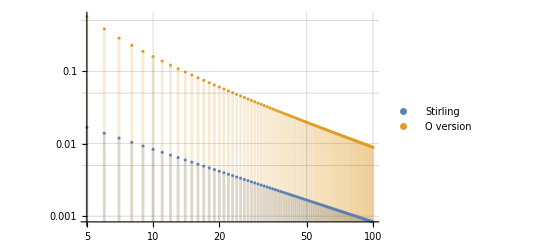

```mathematica
DiscretePlot[{Abs[1-(n!)/(√(2π n)(n/ⅇ)^n)],Abs[1-Log[n!]/(n Log[n]-n)]},{n,5, 100},
PlotRange->All,GridLines->Automatic,ScalingFunctions->{"Log","Log"},
PlotLegends->{"Stirling","O version"}]
```

### What is “erf(x)”? What does it look like for large

Well Wiki and Mathematica (and everyone else agrees that)	
	erf(x)=2/(√π)∫_0^x ⅇ^(-t^2)dt=2/(√π)(x-x^3/3+x^5/10-x^7/42+x^9/216-x^11/1320)+O[x]^13
and we can plot it and see it going to 1 pretty fast.  You actually know some values of erf!

```mathematica
TabView[{
"erf(x)"->Plot[Erf[x],{x,0,4}],
"erf(z)"->ComplexPlot3D[Erf[z],{z,0,4+I},
PlotLegends->Automatic,PlotRange->All]
}]
```

12

You can not efficiently use the TS to compute accurate values for erf(100) or even erf(10).   We are going to learn how to make the useful “asymptotic” but not convergent expansion  
	erf(x)=1-(ⅇ^(-x^2))/(x √π)(1-1/(2 x^2)+(1*3)/((2 x^2)^2)-(1*3*5)/((2 x^2)^3)+…)
as well as a bunch of other “asymptotic” expressions.

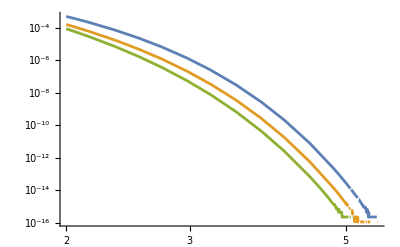

```mathematica
Clear[f1,f2,f3]
f1[z_]:=1-(ⅇ^(-z^2))/(z √π)
f2[z_]:= 1-(ⅇ^(-z^2))/(z √π)(1-1/(2 z^2))
f3[z_]:= 1-(ⅇ^(-z^2))/(z √π)(1-1/(2 z^2)+(1*3)/((2 z^2)^2))
LogLogPlot[{Abs[1-Erf[x]/f1[x]],Abs[1-Erf[x]/f2[x]],Abs[1-Erf[x]/f3[x]]},{x,2,100},PlotRange->All]
```

```mathematica
f2[1.2]
```

0.927285